## 示例：MPO，MPS以及缩并，最好不要更改）

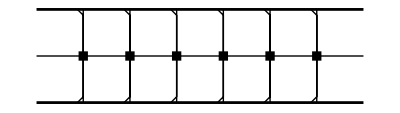

```mathematica
(*Leftcaconical  = Function[{x1,y1,h},Graphics[{Line[{{x1,y1},{x1,y1+h}}],Line[{{x1-1/8*h,y1},{x1,y1+1/8*h}}]}]];*)
ClearAll;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
upleg = Flatten[Table[LeftCaconicalLeg[x,0,1],{x,0,5,1}]];
botleg = Flatten[Table[LeftCaconicalLeg[x,2,-1],{x,0,5,1}]];
mpopart = Table[MatrixProductOperator[x,1,0.1],{x,0,5,1}];
mpopart = Append[mpopart,Line[{{-1,1},{6,1}}]];

Show[Graphics[upleg],Graphics[botleg],Graphics[mpopart],Graphics[{Thickness[0.005],Line[{{-1,0},{6,0}}]}],Graphics[{Thickness[0.005],Line[{{-1,2},{6,2}}]}]]
```

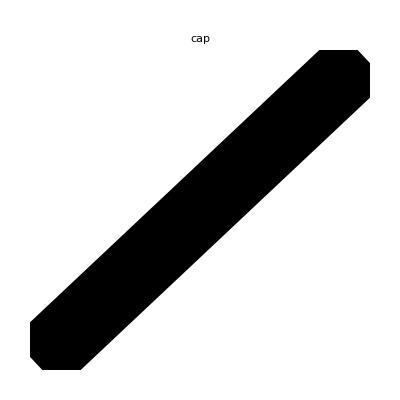

```mathematica
Graphics[{CapForm["Round"],Thickness[.2],Line[{{-1,-1},{1,1}}]},PlotRange->1.5,PlotLabel->cap]
```